#### Function definitions

```mathematica
Clear["Global`*"]
```

```mathematica
k=8.617330 10^-5;(*eV/K*)
Δ=50 10^-6; (*eV*)
α=23.835570319136682;
linspace[start_,stop_,n_:100]:=N[Table[x,{x,start,stop,(stop-start)/(n-1)}]]
gap[T_] := 1-√(2 Pi k T/Δ)Exp[-Δ/(k T)]
f[v_, i0_, r1_, r2_, T_]:=N[i0 gap[T] Im[BesselI[1-I α v /((r1+r2) T),α i0 gap[T]/T]/BesselI[-I α v /((r1+r2) T),α i0 gap[T]/T]]]
fpoints[vlist_, i0_?NumericQ,r1_?NumericQ,r2_?NumericQ, T_?NumericQ]:=N[Table[f[v,i0, r1,r2,T],{v, vlist}]]
vmax=5;
```

#### Load some data sets

```mathematica
dir=NotebookDirectory[]<>"processed_data\\";
idx={1,2,4,6,8,10,12};
temp=IntegerPart@(Identity@@@Import[dir<>"temp.csv"]);
xar={};yar={};
For[ind=1, ind≤Length[idx], ind++,
Print[dir<>ToString[idx[[ind]]-1]<>"x.csv"];
x=Identity@@@Import[dir<>ToString[idx[[ind]]-1]<>"x.csv"];
y=Identity@@@Import[dir<>ToString[idx[[ind]]-1]<>"y.csv"];
xy=Transpose@{x,y};
xy=Select[xy,0<=#[[1]]≤vmax&];
x=N@Transpose[xy][[1]];
y=N@Transpose[xy][[2]];
AppendTo[xar, x]; AppendTo[yar, y];
]
```

C:\Users\rafae\Documents\ZBCP poster\fig\data1\processed_data\0x.csv

C:\Users\rafae\Documents\ZBCP poster\fig\data1\processed_data\1x.csv

C:\Users\rafae\Documents\ZBCP poster\fig\data1\processed_data\3x.csv

C:\Users\rafae\Documents\ZBCP poster\fig\data1\processed_data\5x.csv

C:\Users\rafae\Documents\ZBCP poster\fig\data1\processed_data\7x.csv

C:\Users\rafae\Documents\ZBCP poster\fig\data1\processed_data\9x.csv

C:\Users\rafae\Documents\ZBCP poster\fig\data1\processed_data\11x.csv

#### Plot last dataset

```mathematica
xvals=linspace[0,vmax*1.7, 30];
Manipulate[
res=fpoints[xvals ,i0, r1,r2, T*10^-3];
vvals =xvals-r2*res;
Show[{
ListPlot[Transpose@{vvals,res},PlotRange->{{0,10},{0,i0}},Joined->True],
ListPlot[xy]}]

,{{T,21},10,1000},{{i0,0.035},0.02,0.05},{{r1,50},10,300},{{r2,150},10,300}]
```

Transpose::nmtx: The first two levels of {xvals-150 fpoints[xvals,0.035,50,150,0.185],fpoints[xvals,0.035,50,150,0.185]} cannot be transposed.

Transpose::nmtx: The first two levels of {xvals-150. fpoints[xvals,0.035,50.,150.,0.185],fpoints[xvals,0.035,50.,150.,0.185]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{xvals-150. fpoints[xvals,0.035,50.,150.,0.185],fpoints[xvals,0.035,50.,150.,0.185]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Transpose[{xvals-150 fpoints[«5»],fpoints[xvals,0.035,50,150,0.185]}],PlotRange→{{0,10},{0,0.035}},Joined→True],ListPlot[xy]}].

```mathematica
Manipulate[Show[{
Plot[f[v ,i0, r1,r2, T*10^-3],{v,0,vmax*2},PlotRange->{0,i0},PlotPoints->10,MaxRecursion->2],
ListPlot[Transpose@{N[x+r2 y],y}]}]

,{{T,21},10,1000},{{i0,0.035},0.02,0.05},{{r1,50},10,300},{{r2,150},10,300}]
```

Plot::plln: Limiting value 2 vmax in {Charting`Private`pvar$8070,0,2 vmax} is not a machine-sized real number.

Transpose::nmtx: The first two levels of {{-7.812+150. y,-7.728+150. y,-7.644+150. y,-7.56+150. y,-7.476+150. y,-7.392+150. y,«39»,-4.032+150. y,-3.948+150. y,-3.864+150. y,-3.78+150. y,-3.696+150. y,«137»},y} cannot be transposed.

ListPlot::lpn: Transpose[{{-7.812+150. y,-7.728+150. y,-7.644+150. y,-7.56+150. y,-7.476+150. y,-7.392+150. y,«39»,-4.032+150. y,-3.948+150. y,-3.864+150. y,-3.78+150. y,-3.696+150. y,«137»},y}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[f[v,FE`i0$$490,FE`r1$$490,FE`r2$$490,(FE`T$$490)/10^3],{v,0,vmax 2},PlotRange→{0,FE`i0$$490},PlotPoints→10,MaxRecursion→2],ListPlot[Transpose[{{-7.812+Times[«2»],-7.728+Times[«2»],-7.644+Times[«2»],«45»,-3.78+Times[«2»],-3.696+Times[«2»],«137»},y}]]}].

Plot::plln: Limiting value 2 vmax in {Charting`Private`pvar$8160,0,2 vmax} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[f[v,FE`i0$$490,FE`r1$$490,FE`r2$$490,(FE`T$$490)/10^3],{v,0,vmax 2},PlotRange→{0,FE`i0$$490},PlotPoints→10,MaxRecursion→2],ListPlot[Transpose[{{-7.812+Times[«2»],-7.728+Times[«2»],-7.644+Times[«2»],«45»,-3.78+Times[«2»],-3.696+Times[«2»],«137»},y}]]}].

#### Define optimization function and minimze, plot the minimized result

```mathematica
mf[i0_?NumericQ,r1_?NumericQ,r2_?NumericQ]:=∑_(i=1)^Length[idx] N[ (Norm[ yar[[i]] - fpoints[xar[[i]]+r2 yar[[i]], i0,r1, r2, 10^-3 temp[[idx[[i]]]] ] ] )/ Norm[ yar[[i]] ]^2  ]

fp=FindMinimum[{mf[i0, r1, r2]},{{i0,0.0348},{r1,58.6},{r2,88.4}},AccuracyGoal->3]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{7.29543,{i0→0.034797,r1→58.6,r2→88.4}}

```mathematica
s={15,FontFamily->"Times New Roman"};
```

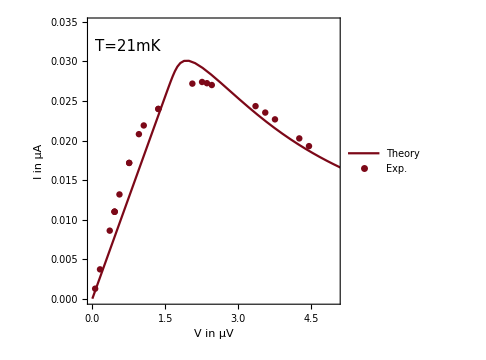

```mathematica
sel=1;
T = temp[[idx[[sel]]  ]]10^-3;
xvals=linspace[0,vmax*2,100];
res=fpoints[xvals ,i0, r1,r2, T]/.fp[[2]];
vvals =xvals-r2*res/.fp[[2]];
xysel=Transpose@{xar[[sel]],N[yar[[sel]]]};
Show[{
ListPlot[Transpose@{vvals,res},
PlotRange->{{0,vmax},{0,i0/.fp[[2]]}},Joined->True,Frame->True, FrameLabel->{Style["V in μV",s],Style["I in μA",s]},PlotLegends->Placed[{"Theory"},{Scaled[{0.85,0.9}],{0.5,0.5}}],
PlotStyle->ColorData[6,"ColorList"],
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],
ImageSize->Medium,
Epilog->{Text[Style["T="<>ToString[temp[[idx[[sel]]]]]<>"mK",s],Scaled[{0.16,0.9}]]}
],

ListPlot[xysel,PlotLegends->Placed[{"Exp."},{Scaled[{0.85,0.8}],{0.5,0.5}}],PlotStyle->ColorData[6,"ColorList"]]
}]
```

#### Save fits for all temperatures

```mathematica
folder=NotebookDirectory[]<>"fits\\";
Imaxfit={};
Imaxexp={};
For[i=1, i ≤Length[temp], i++,
x=Identity@@@Import[dir<>ToString[i-1]<>"x.csv"];
y=Identity@@@Import[dir<>ToString[i-1]<>"y.csv"];

xy=Transpose@{x,y};
xy=Select[xy,0<#[[1]]<=5&];
x=N@Transpose[xy][[1]];
y=N@Transpose[xy][[2]];

xysel=Transpose@{x,N[y*1000]};

T = temp[[i]] 10^-3;

xvals=linspace[0,vmax*2,100];
res=fpoints[xvals ,i0, r1,r2, T]/.fp[[2]];
vvals =xvals-r2*res/.fp[[2]];
AppendTo[Imaxfit, Max[res]];
AppendTo[Imaxexp, Max [N[y]]];
Export[folder<>"res"<>ToString[i-1]<>".pdf",

Show[{
ListPlot[Transpose@{vvals,res*1000},
PlotRange->{{0,vmax},{0,i0*1000/.fp[[2]]}},Joined->True,Frame->True, FrameLabel->{Style["V in μV",s],Style["I in nA",s]},PlotLegends->Placed[{"Theory"},{Scaled[{0.85,0.9}],{0.5,0.5}}],
PlotStyle->ColorData[6,"ColorList"],
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],
ImageSize->Medium,
Epilog->{Text[Style["T="<>ToString[T 10^3]<>"mK",s],Scaled[{0.16,0.9}]]}
],

ListPlot[xysel,PlotLegends->Placed[{"Exp."},{Scaled[{0.85,0.8}],{0.5,0.5}}],PlotStyle->ColorData[6,"ColorList"]]
}]

]
]
```

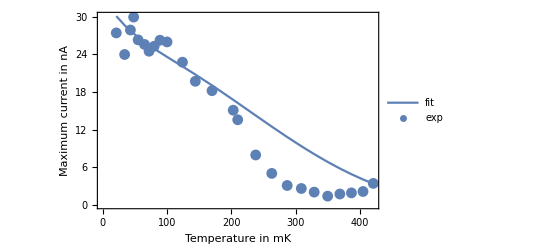

C:\Users\Rafael\Desktop\Dirac_NS_junction\Supercurrent\data1\fits\maxi.pdf

```mathematica
mc=Show[{ListPlot[Transpose@{temp,Imaxfit*1000},Joined->True,Frame->True,FrameLabel->{"Temperature in mK","Maximum current in nA"},PlotLegends->{"fit"}],
ListPlot[Transpose@{temp,Imaxexp*1000},Joined->False,PlotLegends->{"exp"}]},LabelStyle->Directive[FontSize->15,Bold]]
Export[folder<>"maxi.pdf",mc]
```

#### BCS gap temperature dependence

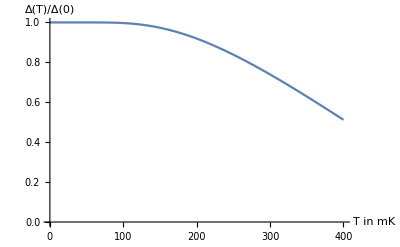

```mathematica
ppp=Plot[gap[T/1000],{T,0,400},PlotRange->{0,1},AxesLabel->{"T in mK","Δ(T)/Δ(0)"}]
```

```mathematica
Export["C:\\Users\\Rafael\\Desktop\\BCS.pdf",ppp]
```

C:\Users\Rafael\Desktop\BCS.pdf

```mathematica
SystemOpen["C:\\Users\\Rafael\\Desktop\\BCS.pdf"]
```

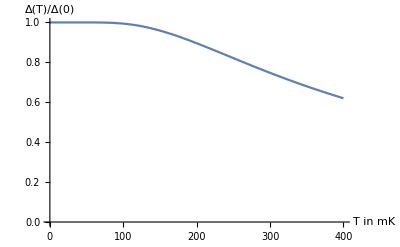

```mathematica
ppp=Plot[Tanh[(50 10^-6)/(2 k (T/1000))],{T,0,400},PlotRange->{0,1},AxesLabel->{"T in mK","Δ(T)/Δ(0)"}]
```